Last modified on: Tuesday, July 10, 2018 at 2:17

Author Info

Luis Antonio Vasquez Reina

Jonathan Gorard

Pontifical Catholic University of Peru - PUCP

Poster Session Content

Symbolic Computation with Infinite Lists

Computer languages are usually constrained to lists of finite size subjected to operations. For example, one may join, partition, sum, or nest them, and get a finite list as a result. 
Even though explicit infinite lists cannot be implemented in a computer, in this project I aim to provide the Wolfram Language with a symbolic calculus for lists of infinite length.
That is, one would be able to treat expressions referring to infinite lists as arguments of operations, e.g, the infinite list of the roots of the natural numbers. The implementation of this kind of operation to the Wolfram Language is the objective of my project.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics--Graphics--Graphics-

I have extended most of the basic Mathematica functions for lists to infinite lists through symbolic manipulation, though partial explicit numerical results can be obtained.
Two non trivial applications of this results are the capacity to define infinite graphs, and to work with Cellular Automata with an infinite initial condition.

It is still pendant to extend other Mathematica functions for finite lists to work with this project’s approach for infinite lists in an optimal way. Also, an implementation could be explored for systems that in principle accept infinite initial conditions.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Basic Operations with Infinite Lists

Many of the basic operations on lists now have a version for infinite lists!

First, I import the package and define the infinite list of the cubes of the integer

Get[FileNameJoin[{NotebookDirectory[],"InfiniteLists.m"}]];
cubes=InfiniteList[0,x↦x^3];
(*showing the first five element on both sides*)
InfiniteTake[cubes,{-5,5}]

{-125,-64,-27,-8,-1,0,1,8,27,64,125}

One can reverse this list, or drop all the negative cubes.

InfiniteReverse[cubes]//InfiniteTake[#,{-5,5}]&
InfiniteDrop[cubes,{-Infinity,-1}]//InfiniteTake[#,5]&

{125,64,27,8,1,0,-1,-8,-27,-64,-125}

{1,8,27,64,125}

Here, I make the range from 1 to infinity, and select the infinite list of the primes

InfiniteSelect[ InfiniteRange[1,Infinity],PrimeQ] //InfiniteTake[#,5]&

{2,3,5,7,11}

Matrices and graphs

With the help of infinite lists, it is possible to work with matrices, which are nested infinite lists.

myInfiniteMatrix=
InfiniteMatrix[{i,j}↦"[row "<>ToString[i]<>",col "<>ToString[j]<>"]"];
(*Take the first rows and columns*)
InfiniteTake[myInfiniteMatrix,2,3]//MatrixForm
InfiniteTake[myInfiniteMatrix,4,4]//MatrixForm

([row 1,col 1] | [row 1,col 2] | [row 1,col 3]
[row 2,col 1] | [row 2,col 2] | [row 2,col 3])

([row 1,col 1] | [row 1,col 2] | [row 1,col 3] | [row 1,col 4]
[row 2,col 1] | [row 2,col 2] | [row 2,col 3] | [row 2,col 4]
[row 3,col 1] | [row 3,col 2] | [row 3,col 3] | [row 3,col 4]
[row 4,col 1] | [row 4,col 2] | [row 4,col 3] | [row 4,col 4])

Infinite matrices allow us to work with infinite graphs!
We can consider the graph with vertices the natural numbers, and where every number is connected its divisors

myGraphMatrix=InfiniteMatrix[{x,y}↦If[Mod[x,y]==0,1,0]];
Table[GraphPlot[ 
InfiniteTake[myGraphMatrix,n,n],
VertexLabeling→True,DirectedEdges→True],
{n,4,9}]

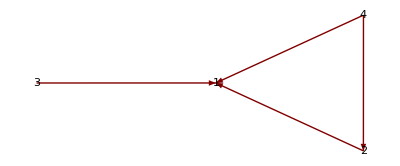
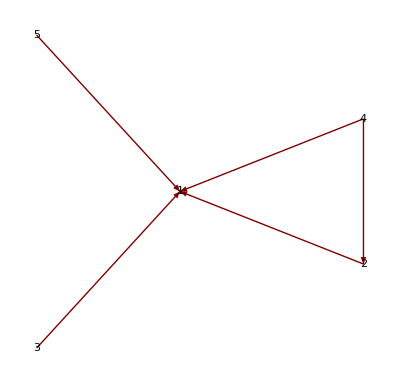
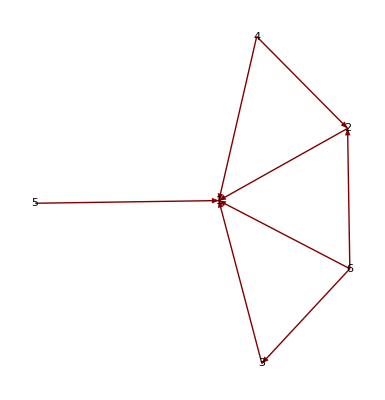
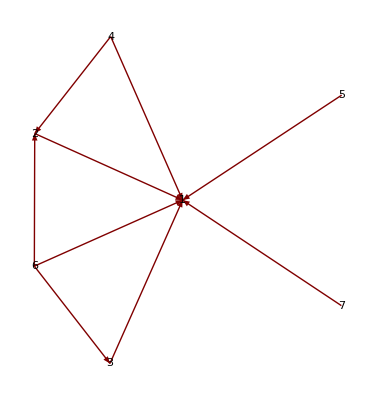
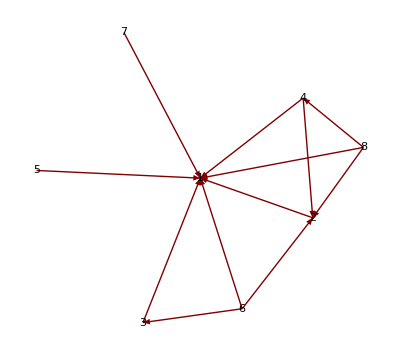
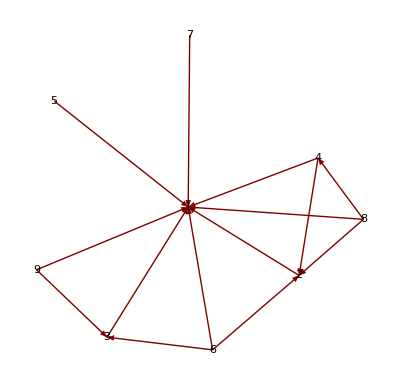

Applications to Cellular Automata

A neat application is that now we can have Cellular Automata that admit infinite initial conditions!
For example, rule 90 gives interesting results:

(*Initial condition with a black cell every 7 cells*)
myInitialCondition=InfiniteList[0,x↦If[Mod[x,7]==0,1,0]];
(*With a widht of 40 cells to either side, plot the first 10 steps*)
InfiniteCellularAutomatonPlot1[90,myInitialCondition,40,10]

-Graphics-

There are differences  if one uses the implemented Cellular Automata function with a similar but finite initial condition. Notice the extremes of the images below.

(*with infinite initial condition*)
-Graphics-
(*with finite initial condition*)
-Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

One can load the package with the following command:

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"InfiniteLists.m"}]]
```

General Introduction

Main idea: Infinite lists are treated as symbolical objects within the Wolfram Language. All infinite lists are countable infinite. An infinite list consists of two components, a direction and a rule that generates its elements. Elements can be of any Head.
With this approach, one can think of the infinite list as “lazily” implemented, i.e,  values are only computed when explicitly asked for. 
By far, the most complicated part of the project was to figure out the constructions needed for the generating rules for the new infinite lists that result from manipulating (applying functions) to infinite lists.
Note that, thanks to functions that insert a finite amount of elements to the list, strictly speaking the generating rule is only needed for the elements in the tail of the infinite list.
After the basic implementation was completed, infinite matrices were quickly available, via nesting of infinite lists and some modification of the already implemented functions of the project. With this,  the implementation of graphs with an infinite number of nodes and infinite adjacent matrices was possible. 
1- dimensional Cellular Automata with infinite initial conditions become available. Though the implementation here is still inefficient, it respects the spirit of cellular automata, which is that the value of a cell depends locally on the cells above it.

Technical Introduction

Infinite lists are objects: InfiniteList[direction,rule].
There are three types of infinite lists:
direction 1 lists  : open on the right side, closed on the left side. 	Example: {1,2,3,4,5,....}
direction -1 lists: open on the left side, closed on the right side. 	Example: {....,-5,-4,-3,-2,-1}
direction 0 lists  : open on both sides: 						Example: {...,-3,-2,-1,0,1,2,---}

Most functions take one or more infinite lists as input and return an infinite list as output. Some of these operations change the direction and most of them change the generating rule.

List of all functions and objects implemented:
(Still inefficient implementations are marked with “ * ”. A “-” is added for ease of reading, but is not included in the name of the function or object )

Infinite-List
Infinite-Prepend
Infinite-Append
Infinite-Part
Infinite-Take
Infinite-Length
Infinite-Drop
Infinite-First
Infinite-Last
Infinite-Direction
Infinite-Range
Infinite-Reverse
Infinite-Join
Infinite-RealDigits*
Infinite-Rest
Infinite-Most
Infinite-Riffle
Infinite-SelectRule
Infinite-Select*
Infinite-Cases*
Infinite-Rule
Infinite-FirstPosition
Infinite-Unequal
Infinite-Plus
Infinite-Times
Infinite-Sum
Infinite-Unequal*
Infinite-And
Infinite-And2*
Infinite-Or
Infinite-Matrix
Infinite-MatrixPlus
Infinite-MatrixTimes
Infinite-PolyTimes
Infinite-CellularAutomatonStep*
Infinite-CellularAutomaton
Infinite-CellularAutomatonData1*
Infinite-CellularAutomatonPlot1*
Infinite-CellularAutomatonData2
Infinite-CellularAutomatonPlot2

A lot of functions return a Failure object if they are called with the wrong arguments.
Specifically: InfinitePrepend, InfiniteAppend, InfinitePart, InfiniteTake, InfiniteDrop, InfiniteFirst, InfiniteLast, InfiniteJoin, InfiniteRest, InfiniteMost, InfiniteEqual

#### Code

Provide one of:

Link to the GitHub: https://github.com/LuisAVasquez/Summer2018Starter

see under "project-notebooks" folder for the progressive advance of the project

The package “Infinite Lists” includes the code for all the functions implemented in this project

#### Written Content / Lesson Plans

Does not apply.

#### Conclusions in Detail

A lot of the basic WL operations for lists have been successfully implemented for infinite lists. Yet, it can be difficult to figure the syntax to use this functions.
There are still many inefficient implementations which could be perfected.
The successful work with infinite matrices and Cellular Automata with infinite initial conditions suggest that infinite lists are a worthy implementation into the Wolfram Language.

#### All Visualizations

Visualizations are not needed for the project, only for examples.

#### Data Sources Links/References

Does not apply.

#### Future Directions

- Extend the existing Mathematica functions to work with infinite lists, and optimizing these extensions.
- Use infinite lists to implement Turing Machines, Tag Systems, and other systems that in principle can accept infinite lists.

#### Background Info Links/References

Some inspiration for this implementations comes from Haskell’s treatment of infinite lists. See:
https://wiki.haskell.org/Why_Haskell_matters#Laziness
Hilbert’s Infinite Hotel is a helpful thought experiment for understanding the behaviour that infinite sets can have. See:
https://en.wikipedia.org/wiki/Hilbert%27s_paradox_of_the_Grand_Hotel

#### Keywords

Provide keywords as items

Infinite Lists

Infinite Graphs

Infinite Cellular Automata

Extensions of lists

Infinite Arguments

#### Other information